## Book Problems

### Chapter 9, Problem 11

### Chapter 10, Problem 5

## Additional Problems

### Problem 1

```mathematica
sol=Assuming[x>=0,DSolveValue[{-u''[x]+u[x]==DiracDelta[x]},u[x],x]]/.{C[1]->1/2,C[2]->0}//FullSimplify//TrigExpand
∫_(-∞)^∞ ((-D[sol, x,x]+sol)f[x])ⅆx
```

ⅇ^x/2+1/2 ⅇ^-x HeavisideTheta[x]-1/2 ⅇ^x HeavisideTheta[x]

f[0]

```mathematica
lapeq=LaplaceTransform[-u''[x]+u[x]==DiracDelta[x],x,s]
lap=SolveValues[lapeq,LaplaceTransform[u[x],x,s]][[1]]/.{u[0]->C[1],u'[0]->C[2]}
InverseLaplaceTransform[lap,s,x]//FullSimplify
```

LaplaceTransform[u[x],x,s]-s^2 LaplaceTransform[u[x],x,s]+s u[0]+u'[0]==1

(-1+s C[1]+C[2])/(-1+s^2)

C[1] Cosh[x]+(-1+C[2]) Sinh[x]

0

1

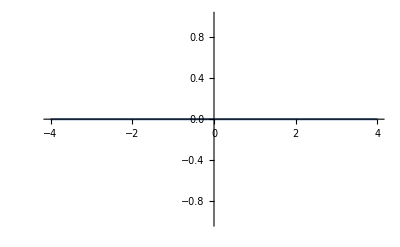

```mathematica
ϕ[x_]=1/2 ⅇ^(-√(x^2));
∫_(-∞)^∞ ((-ϕ''[x]+ϕ[x])f[x])ⅆx
∫_(-∞)^∞ ϕ[x]ⅆx
Plot[{ϕ[x]-1/2(ⅇ^x-HeavisideTheta[x] ⅇ^x+HeavisideTheta[x] ⅇ^-x)},{x,-4,4}]
```

```mathematica
ϕ[x_]=1/2 ⅇ^(-√(x^2));
∫_(-∞)^∞ ϕ[x]ⅆx
∫_(-∞)^∞ (-D[ϕ[x], x,x]+ϕ[x])ⅇ^x ⅆx
```

1

0

### Problem 2

#### (a)

```mathematica
Manipulate[Show[{Graphics[Point[{x/Norm[x]^2,x}],PlotRange->5{{-1,1},{-1,1}}],ContourPlot[x1^2+x2^2==1,{x1,-2,2},{x2,-2,2}]}],{{x,{1,1}},Locator}]
```

```mathematica
GD2[x_,y_]=1/(4π)(1/Norm[x-y]-1/Norm[x/Norm[x]-y Norm[x]]);
Plot3D[GD2[{x,y},{1.5,0}],{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},1<x^2+y^2]]
```

-Graphics3D-

```mathematica
∇_{x1,x2,x3}^2 GD2[{x1,x2,x3},{1,0,0}]//FullSimplify
```

```mathematica
∇_{x1,x2,x3}^2 GD2[{x1,x2,x3},{1,0,0}]//FullSimplify
```

```mathematica
DSolveValue[{v''[r]+2/r v'[r]==0,v[1]==0},v[r],r]
```

((-1+r) C[1])/r

```mathematica
f[x_,y_,z_]=1-1/(√(x^2+y^2+z^2));
Assuming[x∈Reals&&y∈Reals&&z∈Reals,{f[x,y,z],∇_{x,y,z}^2 (f[x,y,z])}//FullSimplify]
Plot3D[{f[x,y,0],Evaluate[∇_{x1,y1}^2 f[x1,y1,0]]/.{x1->x,y1->y}},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2>=1],PlotRange->All]
```

{1-1/(√(x^2+y^2+z^2)),0}

-Graphics3D-

### Problem 3

### Problem 4

```mathematica
-D[√((-x1-y1)^2+(-x2-y2)^2), y1]
```

(-x1-y1)/(√((-x1-y1)^2+(-x2-y2)^2))